5 Acid/ Base Chemistry

Robert R. Gotwals, Jr

NCSSM Chemistry

## Section 1: Acid/Base Basics

In Chapter 4, we discussed drug solubilities, and the reader should know that there are basically two environments in the body:  aqueous (water-based) and lipid ("fats").  Any time you have molecules in an aqueous environment, issues related to acid/base chemistry are often important.  In all likelihood, you have studied acid/base chemistry in an introductory chemistry course.  Some of those concepts are revisited here, and then we apply them to medicinal chemistry problems.

There are a number of different definitions and descriptions for what is an acid and what is a base.  You might have encountered these two ideas:

Brönsted-Lowry:  this model defines acids as proton donors (H^+) and bases as proton acceptors.  Beginning chemistry students typically encounter a proton donor as something like hydrochloric acid (HCl), where the proton (H^+) can dissociate from the chlorine.  The H^+ is the acidic part of this compound.  Likewise, we will often designate a base as a compound tha contains a hydroxy or hydroxyl ion, (OH^-).  The classic example of a base is NaOH:

Acid:  HCl ⇄ H^+ + Cl^-

Base:  NaOH ⇄ Na^+ + OH^-

The bidirectional arrow in these reactions means that molecule moves back and forth between the molecule and the separated ions.

Lewis Acid/Base:  in this model, acids are electron pair acceptors and bases are electron pair donors.  This model is very useful in reaction chemistry, and is used heavily in organic, computational, and medicinal chemistry.

Specific acids (and bases) have a value associated with them known as the dissociation constant, abbreviated K_a for the acid dissociation constant or K_b for the base dissociation constant.  The larger the value of K_a, the more likely it is that the molecule will be dissociated, that is, in ionic form, and hence, more acidic.  In medicinal chemistry, we talk about the un-ionized form of the molecule (HCl) or the ionized form (H^+ + Cl^-) of the molecule.  The larger the K_a, the more acidic the molecule.  Because the values for K_a tend to be very large or very small numbers, we apply a little mathematics called "p".  Using the general equation shown in Equation 1.1:

pX = -log(X)

where X is some measured property.  So, as shown in Equation 1.2:

pK_a = -log(K_a)

Because of the negative logarithm, the smaller the pK_a, the more acidic the molecule is.

You may also be familiar with the pH scale.  pH is a measure of the concentration of hydrogen ions (protons), and we use the notation [H^+] to signify the concentration of acidic hydrogens in a solution (remember, this chemistry all happens in liquid, typically water).  So, pH is defined as shown in Equation 1.3:

pH = -log[H^+]

pH values run from 1 to 14, with a pH=7 being defined as "neutral", and values less than 7 as acidic, greater than 7 as basic.  The pH value of a particular acid is not always constant, whereas the pK_a of an acid is always a constant value. The two values -- pH and pK_a -- are related, and for weak acids we can use the Henderson-Hasselbalch equation shown in Equation 1.4 to relate the two:

pH =pK_a+ log([Ionized form]/[Un-ionized form])

For example, if we have the reaction shown below:

HA ⇄ H^+ + A^-

the H-H equation is shown in Equation 1.5:

pH =pK_a+ log([A^-]/[HA])

In medicinal chemistry, what we often wish to know is the percent ionization, or what fraction of the acid is ionized and what fraction is not.  We can use the question shown in Equation 1.6:

Percent ionization = 100/(1+10^(±pH+pKa))

This equation is generated by algebraically re-arranging the Henderson-Hasselbalch equation; the 100 in the numerator ensures that the resulting answer is reported as a percentage.  Notice that the answer depends upon the pH (which varies) and the pK_a (which does not).  Notice too the "±" sign in front of pH.  The choice of positive or negative depends upon whether the drug in question is an acidic drug or a basic drug.  Identifying drugs as acidic or basic is discussed in the next section.  In medicinal chemistry, we will want to know whether the drug is mostly in ionized form or un-ionized form.  As shall be shown in a subsequent section, the percent ionization value determines where the drug will go in the body.  Given that there are different pH environments in the body, the value of the percent ionization depends greatly on where the drug goes.

## Section 2: Identifying Drugs as Acidic/Basic

Drugs can sometimes be categorized or classified as being acidic or basic.  Figure 1 shows some example drugs, such as penicillin and caffeine (yes, it's definitely a drug!) and their classifications as acidic or basic drugs.  Many drugs have both an acidic and basic nature, so identifying a drug as acidic or basic is sometimes a challenge.  In the table, the acidic drugs are listed from the strongest acidic drug (penicillin) to the weakest (AZT), while the basic drugs are listed from the weakest (caffeine) to strongest (amphetamine).  In the reaction mechanism for acidic drugs, the proton leaves the HA molecule and attaches to a water molecule, forming a hydronium ion.  This is simply another form of the H^+ ion, and is very commonly used, given that these reactions happen in water.  Likewise for the basic reaction:  water is shown as part of the reaction mechanism.

-Graphics-

Figure 1:  Examples of acidic and basic drugs

There are some general guidelines for identifying whether or not a drug is acidic or basic.  The easiest way is to identify the carboxylic acid (COOH) functional group.

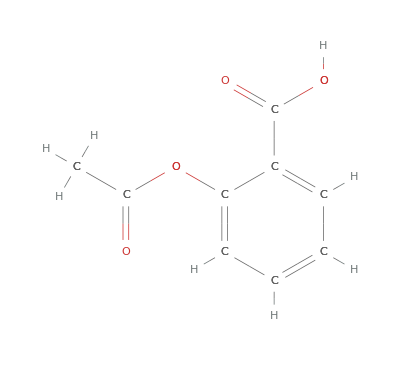
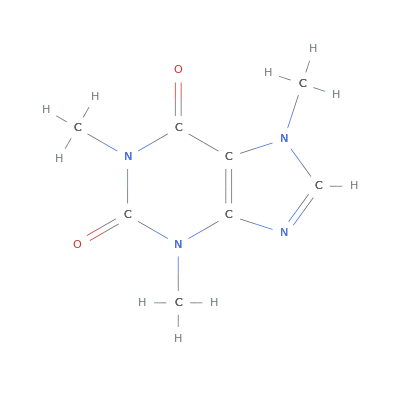
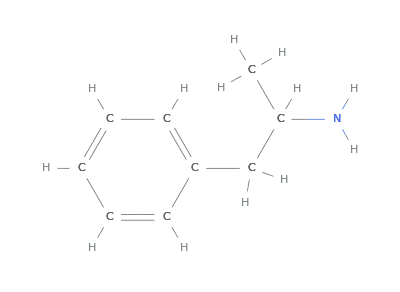
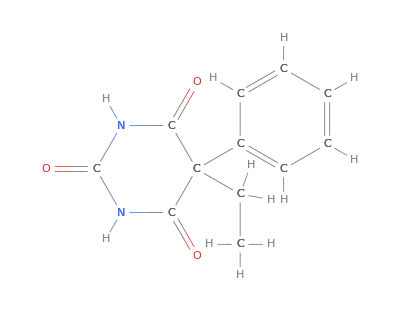
Drug | Type | Structure | Description
Aspirin | Acidic | -Graphics- | The carboxylic acid
attached to the benzene ring
strongly suggests that aspirin
is an acidic drug
Caffeine | Basic | -Graphics- | The presence of one or more
amine functional groups typically
is indicative of a basic drug
Amphetamine | Basic | -Graphics- | Again, a primary amine functional
group is what makes this drug a
basic drug
Phenobarbital | Acidic | -Graphics- | This one is a little more difficult.
It contains amines, but it also contains
carbonyls (C=O).  The hydrogens on the
nitrogen atoms are likely to dissociate,
partly due to the presence of the double-
bonded oxygens

Drugs can also be what is known as amphoteric.  This means that they have at least one acidic functional group (such as a carboxylic acid) and at least one basic functional group (such as an amine).  Drugs that are amphoteric typically have more than one pK_a value.  Figure 2 shows a screensnap for the drug amoxicillin, an amphoteric drug.  Notice the presence of both the amine functional group (shown in blue) and two acidic hydrogens, one on the carboxylic acid and one on the hydroxy group (shown in red).  Notice also that there are two pK_a values, one for the acid and one for the base.

-Graphics-

Figure 2:  pKa data for amoxicillin, an amphoteric drug (Source:  ADME/Tox Weboxes)

## Section 3: Application of Acid/Base Chemistry in Drug Design

One of the primary uses of acid/base chemistry in medicinal chemistry is in helping to determine if a drug is water- or lipid-soluble, or, hydrophilic vs. hydrophobic.  As described in Section 2, drugs are generally categorized as acidic or basic (for purposes of this discussion, we will not include amphoteric drugs).  If an acidic drug is placed into an acidic pH environment (such as the stomach), the drug will not ionize (dissociate); it will stay as a complete molecule.  The same drug in a basic environment (such as the small intestine) will ionize.  We can now apply this general rule:

Non-ionized drugs are hydrophobic (conversely, lipophilic) and will be soluble in a lipid environment

Ionized drugs are hydrophilic (conversely, lipophobic) and will be soluble in an aqueous environment

This is shown in Figure 3:

-Graphics-

Figure 3  Chart of acidic/basic drugs and pH environment

Another way of describing this is as follows:

Hydrophilic molecules are typically charged compounds that are soluble in water

Hydrophobic molecules are typically neutral compounds that are soluble in lipds, and will cross most cell membranes

The graphic in Figure 3 looks to help describe the effects of ionization vs. non-ionization.  The acidic drug aspirin is shown as the example.  In the stomach, with a pH of 2.0, the drug is mostly non-ionized.  We can show this by using the formula for percent ionization:

Percent ionization = 100/(1 + 10^(-(pH-pKa)))

From the chart above, we see that aspirin has a pKa of 3.5.  In the stomach, we determine that approximately 3% of the drug is in the ionized form:

```mathematica
PercentIonization=100/(1+10^(-(2.0-3.5)))
```

3.06534

Conversely, the same drug in the bloodstream (slightly basic at pH=7.4), the majority of the drug (99.99%) is in the ionized form:

```mathematica
PercentIonization=100/(1+10^(-(7.4-3.5)))
```

99.9874

In the intestines (pH=5.5, weakly acidic), we get approximately 99% ionization:

```mathematica
PercentIonization=100/(1+10^(-(5.5-3.5)))
```

99.0099

The direction of the ionization is shown by the size of the arrows.  A larger, bolder arrow says that the drug is in the form being pointed at by the larger arrow, for example, non-ionized (97%) in the stomach.  Because aspirin in the stomach is non-ionized, it is hydrophobic/lipophilic, and thus able to easily cross the lipid cell membranes to enter the blood.  In the intestines, some of the non-ionized compound can cross the cell membrane into the bloodstream, but the graphic and the mathematics strongly suggests that aspirin is entering the bloodstream primarily by crossing the lipid membrane in the stomach.

-Graphics-

Figure 4:  Graphic of majority forms of a drug in three compartments -- stomach, intestine, and blood

The beginning medicinal chemist, therefore, needs to be able to perform this analysis:

Given:

the acid/base nature of the drug (is it acidic or basic?)

the pKa of the drug

the pH of the environment into which the drug is going

be able to predict:

whether the majority form of the drug is ionized or non-ionized

whether the majority form of the drug is hydrophilic or hydrophobic

be able to state whether the drug will cross a cell membrane, which depends on how the drug is administered

For purposes of this chapter, we define three ways in which a drug might be administered.  There are more ways, but these four capture the essence of the major methods.  Note that intravenous (IV) administration is less concerned with acid/base effects, since the drug is by definition delivered directly to the bloodstream, so we are less concerned about the ability of the drug to cross cell membranes!

Oral (PO, per orum):  as shown in Figure 4, drugs administered orally are primarily non-ionized, and as such are hydrophophic, and can cross the lipid cell membrane

Subcutaneous (SQ, under the skin):  these drugs are majority form ionized, and as such are soluble in an aqueous environment, and as such are hydrophilic

Intramuscular (IM):  these drugs are primarily non-ionized, are hydrophobic, and can cross the lipid cell membranes to get into the bloodstream